Quantum Phase Estimation |

Definitionpaclet:Q3/tutorial/QuantumPhaseEstimation#50473190 | Accuracypaclet:Q3/tutorial/QuantumPhaseEstimation#1752851100
Quantum Implementationpaclet:Q3/tutorial/QuantumPhaseEstimation#2130649800 | Simulation of von Neumann Measurementpaclet:Q3/tutorial/QuantumPhaseEstimation#294899827
Examplepaclet:Q3/tutorial/QuantumPhaseEstimation#660511198 |

See also Section 4.4 of the Quantum Workbook (Springer, 2022)https://doi.org/10.1007/978-3-030-91214-7.

Quantum phase estimation is a procedure to estimate the phase of the unknown eigenvalue of an eigenstate of a unitary operator. Like the quantum Fourier transformation, the quantum algorithm for the quantum phase estimation is one of the key elements of many quantum algorithms, including the quantum factorization algorithm. In fact, the quantum Fourier transform is a part of the quantum phase estimation algorithm, and it almost always appears in that way rather than independently. In this sense, the quantum phase estimation is a key subroutine for most quantum algorithms. Indeed, all quantum algorithms known so far can be regarded as a quantum phase estimation in one form or another. (Mathematically, they belong to the class called the hidden subgroup problem.)

Hadamardpaclet:Q3/ref/HadamardQ3 Package Symbol | The Hadamard gate.
ControlledUpaclet:Q3/ref/ControlledUQ3 Package Symbol | The controlled-unitary gate.
QFTpaclet:Q3/ref/QFTQ3 Package Symbol | Represents the quantum Fourier transform.

Q3 functions useful in the quantum phase estimation procedure.

Make sure that the Q3 package is loaded to use the demonstrations in this documentation.

```mathematica
<<Q3`
```

Throughout this document, symbol S will be used to denote qubits and the Pauli operators on them. Similarly, symbol c will be used to denote complex-valued coefficients.

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

Definition

Let U be a unitary operator on the Hilbert space associated with a register consisting of n qubits. Suppose that the quantum register is known to be prepared in an eigenstate state ϕ of U. Its unknown eigenvalue ⅇ^(ⅈ 2π ϕ) is desired. The quantum phase estimation procedure gets the phase value 2π ϕ of the eigenvalue.

Note that the quantum phase estimation is directly related to the measurement. Recall that finding the eigenvalue ⅇ^(ⅈ 2π ϕ) reveals the corresponding eigenstate ϕ. A unitary operator can be written as U=exp(ⅈ 2π Q) for some observable Q, so an estimation of phase corresponds to the measurement of the quantity Q. In this sense, one can regard the quantum phase estimation procedure as a realization of the quantum measurement on quantum computers. We will discuss this aspect in more detail later.

Quantum Implementation

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

### Initialization

To implement the quantum phase estimation procedure, take an auxiliary register of m qubits. We call it the “probe” register, for a reason that will be clear later in this section.

We prepare the probe register in the superposition of all elements in the logical basis by applying the Hadamard gate on every qubit in the probe register,

0→^(H^(⊗m))1/2^(m/2)∑_(x=0)^(2^m-1) x.

Then, the state vector of the total system becomes

(H^(⊗m)0)⊗ϕ=1/2^(m/2)∑_(x=0)^(2^m-1) x⊗ϕ.

### Conditional Exponentiation of Unitary Transformation

Next, perform a unitary transformation on the total system defined by

U_QPE:x⊗y↦x⊗(U^x y) ,

where x (x=0,1,··· ,2^m− 1) belongs to the probe register and y (y=0,1,. . . ,2^n−1) to the native register. The transformation is a conditional exponentiation, performing the unitary transformation U repeatedly depending on value x of the probe register. More explicitly, the conditional exponentiation reads as

x⊗(U^x y)=x_1⊗x_2⊗⋯⊗x_m⊗(U^(x_1 2^(m-1))U^(x_2 2^(m-2))(⋯U)^(x_m 2^0)y) .

This is a product of controlled-U^(2^k) gates controlled by the value x_k of the k^th qubit in the probe register. Thus it is implemented by using the following quantum circuit

-Graphics-

Here, it is worth noting that an efficient quantum phase estimation algorithm requires an efficient implementation of the controlled-U^(2^k) gates for arbitrary integer k. One of the most common unitary transformations that allows for efficient implementation is modular multiplication, defined by

Uy:=a y (mod N)

for a fixed integers a and N. In this case, the product of controlled-U^(2^k) gates leads to the modular exponentiation,

x⊗(U^x y)=x⊗a^x y  (mod N) .

It is known that modular exponentiation can be calculated efficiently. The modular exponentiation (arising from the modular multiplication) is used in the order-finding problem.

Upon the conditional unitary transformation, the state vector becomes

1/2^(m/2)∑_x x⊗(U^x ϕ)=1/2^(m/2)∑_x x⊗(ϕ ⅇ^(-ⅈ2π ϕ))=(1/2^(m/2)∑_x^(2^m-1) x ⅇ^(-ⅈ2π ϕ))⊗ϕ .

Note that the probe register has picked up a relative phase shift proportional to x, ⅇ^(-ⅈ 2π x ϕ), while the original register still remains in the same state ϕ.

### Quantum Fourier Transform

The state stored on the probe register is formally the same as the (inverse) quantum Fourier transform. For the moment, let us assume that ϕ (0 ≤ϕ< 1) takes one of the discrete values

0/2^m,1/2^m,2/2^m,⋯,(2^m-1)/2^m.

In this case, performing a quantum Fourier transform U_QFT on the probe register brings it to the logical basis state 2^m ϕ. A subsequent measurement on the probe register in the logical basis reveals the value ϕ.

In general, the normalized phase ϕ is a continuous parameter and takes values other than the discrete values listed above. In such a case, the number m of the qubits in the probe register is not sufficient to accurately estimate ϕ. Thus, the measurement randomly produces different values. Fortunately, the probability for a particular value is distributed sharply (with a larger probe register resulting in a sharper probability distribution) around the value 2^m ϕ.

To see this, note that the final quantum Fourier transform on the probe register transforms the state as

1/2^(m/2)∑_x^(2^m-1) x ⅇ^(-ⅈ2π ϕ) →^QFT ∑_y y(1/2^m∑_x^(2^m-1) x ⅇ^(-ⅈ2π (y-2^m ϕ)x/2^m)) .

Upon the measurement on the probe register in the logical basis, the probability to get the outcome y is given by

P_y=(|1/2^m∑_(x=0)^(2^m-1) ⅇ^(ⅈ2π(y-2^m ϕ)x/2^m)|)^2=1/2^(2m)(|(1-ⅇ^(ⅈ2π(y-2^m ϕ)))/(1-ⅇ^(ⅈ2π(y-2^m ϕ)/2^m))|)^2.

For a reasonably large m, probability P_y sharply peaks around 2^m ϕ as seen in the following figure (for ϕ=18/25 and m=4). It is precisely 1 only when 2^m ϕ is one of the integers 0,1,2,…,2^m-1, as mentioned above.

-Graphics-

### Summary

Overall, the procedure described above is summarized in the following diagram.

-Graphics-

Example

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

We take an ancillary register consisting of four qubits, which we call the “probe” register.

```mathematica
$m=4; (* the number of qubits in the "probe" register *)
prb=Range[$m]; (* the "probe" register *)
sys=$m+1; (* the "system" register *)
```

We consider a rotation around the z-axis for the unitary operator. In this case, the logical basis consists of the eigenstates of the unitary operator.

```mathematica
ϕ=18/25;
```

Here is the controlled-U^(2^(m-j)) operator to be used in the phase estimation algorithm.

```mathematica
ctrlU[j_]:=ControlledU[S[j],Phase[-2Pi ϕ*Power[2,$m-j],S[sys]],"Label"->Superscript["U",Superscript["2",ToString[$m-j]]],
"LabelSize"->0.65]
```

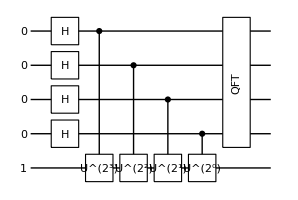

```mathematica
qc=QuantumCircuit[LogicalForm[Ket[],S@prb],Ket[S[sys]->1],{S[prb,6],"LabelSize"->0.8},ctrlU[1],ctrlU[2],ctrlU[3],ctrlU[4],QFT[S@prb]]
```

In this particular example, we already know that the “system” register remains in its initial state and what the initial state is. To make the process general, however, we take the partial trace over the system register to focus on the “probe” register.

```mathematica
out=Matrix[N@qc];
rho=PartialTrace[out,{sys}];
```

From the density matrix of the probe register, we can get the probability to read out the possible values of the normalized phase.

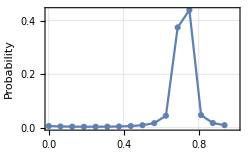

```mathematica
probability=Transpose@{Range[0,2^$m-1]/2^$m,Normal@Chop@Diagonal@rho};g=ListLinePlot[probability,PlotRange->{{0,1},All},PlotMarkers->Automatic,
FrameLabel->{"ϕ","Probability"}]
```

Accuracy

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

Let us now estimate the error bound of the phase estimation. We split 2^m ϕ into the integer part p and the fractional part δ so that 2^m ϕ= p+δ with 0 ≤ δ < 1. The fractional part δ cannot be stored in the m-qubit probe register, and it causes an error in the estimated phase. For a given resource with finite size, we cannot avoid it.

One can get the best estimate when measurement outcome y points correctly to p or p+1. The error ϵ=|y/2^m-ϕ| in the estimated phase would be less than 2^-m. The probability P_y is distributed sharply (for a large m) around p and p+1. The probabilities at y=p and y=p+1 are bigger than those at any other values of y. Therefore, it is useful to bound the probability for the error in the estimated
phase to be less than 2^-m,

P(ϵ<2^-m)=P_p+P_(p+1) .

Unfortunately, the probability distribution P_y has finite width, and outcome y does not always result in the desired value. Nevertheless, P_y for y=p and y=p+1 are bigger than for any other values of y.

Then, it follows that

P(ϵ<2^-m)=1/2^(2m)(|(sin(πδ))/(sin(πδ/2^m))|)^2+1/2^(2m)(|(sin(π(1-δ)))/(sin(π(1-δ)/2^m))|)^2 .

As a function of δ, it is symmetric around δ = 1/2. That is, 1/2 − δ→ δ does not change the expression. Furthermore, it has a maximum of 1 for δ=0 because in this case P_p=1, and no error can arise. It has minimum at δ=1/2 because P_p = P_(p+1) in this case. We thus have the inequality

P(ϵ<2^-m)>=1/2^(2m-1)(|(sin(π/2))/(sin(π/2^(m+1)))|)^2 .

Note that (π/2^(m+1))/sin(π/2^(m+1)) monotonically decreases and converges to 1 as
m increases to infinity. Therefore, we have

P(ϵ<2^-m)>=8/π^2≈0.81 .

As m increases, we can improve the accuracy with error less than 2^-m with success probability larger than 0.81.

Simulation of von Neumann Measurement

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

The von Neumann scheme of measurement is an idealistic mechanism that implements a projection measurement. As already mentioned, the quantum phase estimation procedure is, in spirit, equivalent to the von Neumann scheme of measurement. In fact, the quantum phase estimation was put forward to simulate the von Neumann scheme on quantum computers (Kitaev, 1996, 1997). The equivalence of the von Neumann scheme of measurement and the quantum phase estimation procedure has also inspired direct tomography of wave functions and its variants (Lundeen et al., 2011; Vallone and Dequal, 2016). Therefore, it will be interesting for scientific as well as heuristic purposes to examine the equivalence in more detail.

We consider a “system” consisting of n qubits and pick a “probe” of m qubits. To maintain the physical nature of the von Neumann scheme, let us consider two bases for the probe, {X_x} and {P_x} (x=0,1,2,. . . ,2^m−1), that are conjugate to each other and related by the quantum Fourier transform P_x=U_QFT X_x. We call them the “position” and “momentum” basis, respectively. To simplify the argument, we assume the system to be in a definite yet unknown eigenstate a of an observable A. We want to find eigenvalue a by conducting a measurement procedure.

Following the von Neumann scheme, we prepare the probe in the state X_0, which refers to a definite position. Then, we let the system and probe interact with each other by coupling the “momentum” operator P of the probe to the observable A of the system with strength g. After an interaction for a finite duration of time, the probe is measured in the basis X_y, as illustrated in the following schematic diagram.

-Graphics-

We rewrite the interaction unitary operator as

U_int=exp(-ⅈ g P⊗A)=∑_x P_xP_x⊗ⅇ^(-ⅈ g p_x A)=∑_x P_xP_x⊗U^x ,

where the operator U acting on the system has been defined by

U=exp(-ⅈ((2π g)/2^n)A) .

In this new interpretation, operator U is repeatedly operated x times on the system depending on the wave number p_x (eigenvalue of P) in the probe. This interpretation is seemingly opposite to the original idea in the von Neumann scheme, where the translation operator T is operated on the probe depending on eigenvalue a of A in the system. This reinterpretation is depicted schematically in the following diagram.

-Graphics-

Note that the probe register controls the operation of U on the system in the “momentum” basis {P_y}, and hence the momentum basis is the computational basis (logical basis). On the other hand, the von Neumann scheme requires the measurement to be performed in the “position” basis {X_y}. Any measurement in a basis different from the computational basis can be achieved by applying a proper unitary transformation corresponding to the basis change (see Computational Model of Measurement), which in this case is the quantum Fourier transform. Similarly, one can obtain the input state X_0 by acting U_QFT^† on P_0. These changes lead to the schematic diagram.

-Graphics-

Finally, with all bases changed to the computational basis {P_x}, we can drop the addition labels ‘P’ and ‘p’ from the states and eigenvalues. Recall also that the action of the quantum Fourier transform on P_0 can be replaced by Hadamardpaclet:Q3/ref/HadamardQ3 Package Symbol gates, U_QFT^†P_0=H^(⊗m)P_0. Therefore, the von Neumann measurement can be depicted as in the following diagram, which is identical to a diagram corresponding to the quantum phase estimation procedure.

-Graphics-

| Related Guides
▪Quantum Computation and Quantum Information

| Related Tech Notes
▪Quantum Algorithms
▪Quantum Fourier Transform
▪Measurements on Quantum States
▪Computational Model of Measurement
▪Quantum Computation and Quantum Information with Q3

| Related Links
▪R. Cleve, A. Ekert, C. Macchiavello, and M. Mosca, Proceedings of the Royal Society A 454, 339 (1998)https://doi.org/10.1098/rspa.1998.0164, “Quantum algorithms revisited.”
▪A. Y. Kitaev, Electronic Colloquium on Computational Complexity 3, 3 (1996)http://arxiv.org/abs/quant-ph/9511026, “Quantum measurements and the Abelian Stabilizer Problem.”
▪A. Y. Kitaev, Russian Mathematical Surveys 52, 1191 (1997)https://doi.org/10.1070/RM1997v052n06ABEH002155, “Quantum computations: algorithms and error correction.”
▪J. S. Lundeen, B. Sutherland, A. Patel, C. Stewart, & C. Bamber, Nature 474, 188 (2011https://doi.org/10.1038/nature10120), “Direct measurement of the quantum wavefunction.”
▪G. Vallone and D. Dequal, Physical Review Letters 116, 040502 (2016)https://doi.org/10.1103/physrevlett.116.040502, “Strong Measurements Give a Better Direct Measurement of the Quantum Wave Function.”
▪M. Nielsen and I. L. Chuang (2022)https://doi.org/10.1017/CBO9780511976667, Quantum Computation and Quantum Information (Cambridge University Press, 2011).
▪Mahn-Soo Choi (2022)https://doi.org/10.1007/978-3-030-91214-7, A Quantum Computation Workbook (Springer, 2022).